# Minus-K Scratch Notebook

## Max Freeman

## Initial Notes

jennifer hoffman stm damping

minus k technology stm vibration isolation scanning tunneling microscope
^ paul weiss -author of papers

Rod Lake @ UW Madison

First: Simulate vibrational spectrum of room
Next: Rod Lake’s articles

airleg/pneumatic damping profile
vibrational damping springs

first: room -> airlegs -> spring -> final
next: room -> airlegs -> minus k spring -> final

## Important Links

Air Legs Spec Sheet
Paper on Theory of STM Vibrational Isolation
Less Explicit Paper on Theory of STM Vibrational Isolation
Rod Lakes Minus K Materials
Probably Better Rod Lakes Paper

## Terminology

Stress: Force/Area = F/A

Strain: Change in Length / Length = δL/L_0

Stiffness / Modulus: how much energy must be put into the sample to distort it. E = stress/strain

Damping Capacity: a material’s ability to dissipate elastic strain energy (converting to mechanical energy to heat) during mechanical vibration  ⇒ Energy / Volume.

## Images

-Graphics-

-Graphics-
in units of meters (rms) lol
-Graphics-

## Chamberlain Vibrational Noise Data

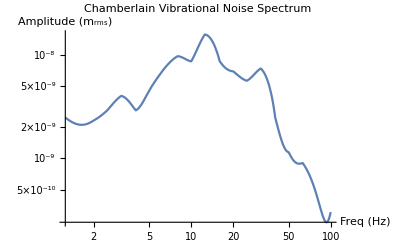

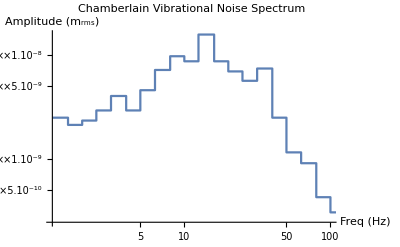

```mathematica
bins = {0,1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {0,200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
unlogch[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
data = Table[unlogch[pixels⟦i⟧],{i, 1, Length[pixels]}];
ifun=Interpolation[Transpose[{bins, data}]];
LogLogPlot[ifun[x], {x,1.25, 100}, PlotLabel->"Chamberlain Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Amplitude (m_rms)"}]
pltnoise = ListStepPlot[Transpose[{bins⟦2;;-1⟧,data⟦2;;-1⟧}], ScalingFunctions->{"Log10", "Log10"}, PlotLabel->"Chamberlain Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Amplitude (m_rms)"}, PlotRange->{{1.25,100},Automatic}]
```

find factor such that vibration is less than a pm, find largest one and return both factor and freq

## Transfer Functions

Note: This is purely for *vertical* vibrations

### Air Legs

-Graphics-

```mathematica
dataim = ImageData[Import["C:\\Users\\freem\\Documents\\GitHub\\MinusKModelling\\Resources\\legs_vert_transf2.bmp"]];
pixelData={};
For[j=1, j≤Dimensions[dataim]⟦2⟧, j++,
x={};
For[i =1 , i≤ Dimensions[dataim]⟦1⟧, i++,
dataim⟦i,j⟧ = dataim⟦i,j,1⟧;
If[dataim⟦i, j⟧≠ 1.,
x = Append[x, i];
];
];
pixelData=Append[pixelData,{j,353-Mean[x]}];
]
tAirLeg ={N[0.8*Power[10,Log10[30/0.8]/462*Transpose[pixelData]⟦1⟧]],N[Power[10,4/353 Transpose[pixelData]⟦2⟧-3]]};
```

(0,10) and (-353,0.001)
-353/4Log[x/10]

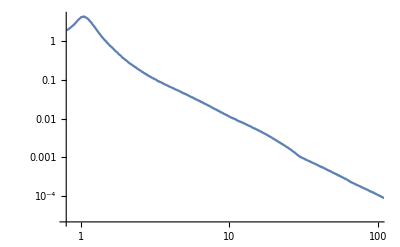

```mathematica
t1 = {tAirLeg⟦1⟧,ifun[tAirLeg⟦1⟧]*tAirLeg⟦2⟧//Quiet};
pltairleg =ListLogLogPlot[Transpose[tAirLeg],Joined->True, PlotRange->{{0.8,100}, All}]
```

### Spring

-Graphics- 
-Graphics-
-Graphics-

ω_0 = 2π*1.07
γ = 0.11*ω_0 = 0.74

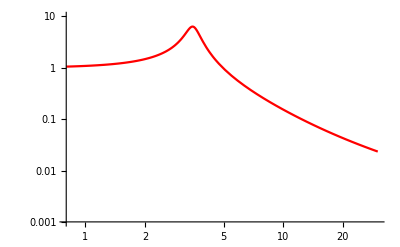

```mathematica
ω0 =2π*3.5;
γ=0.08ω0;
sprtransf[f_]:=(√(4 γ^2(2π f)^6+(ω0^4-ω0^2(2π f)^2+4 γ^2(2π f)^2)^2))/((ω0^2-(2π f)^2)^2+4 γ^2(2π f)^2);
pltspr=LogLogPlot[sprtransf[f], {f, 0.8, 30}, PlotStyle->Red,PlotRange->{{0.8, 30},{0.001,10}}]
```

### Both

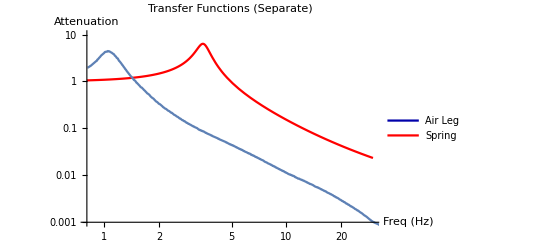

```mathematica
plttrans=Show[pltspr, pltairleg,PlotLabel->"Transfer Functions (Separate)",LabelStyle->13, AxesLabel->{"Freq (Hz)", "Attenuation"},AxesStyle->14, ImageSize-> 400];
plttrans = Legended[plttrans , Placed[LineLegend[{Darker[Blue], Red},{"Air Leg", "Spring"}, LabelStyle->11],Right]]
```

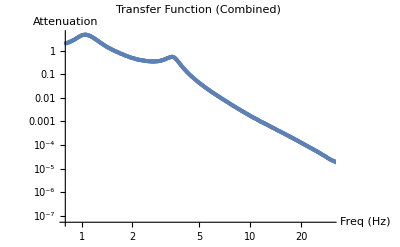

```mathematica
multtransf = Transpose[{tAirLeg⟦1⟧,sprtransf[tAirLeg⟦1⟧]*tAirLeg⟦2⟧}];
imulttransf = Interpolation[multtransf];
plttransmult=ListLogLogPlot[multtransf, PlotLabel->"Transfer Function (Combined)", AxesLabel->{"Freq (Hz)", "Attenuation"}, PlotRange->{{0.8,30},Automatic}]
```

## Resultant Noise

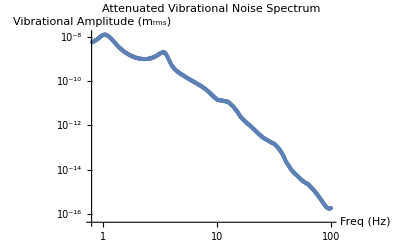

```mathematica
For[i=1,i≤ Length[tAirLeg⟦1⟧],i++,
If[tAirLeg⟦1, i⟧>100,stop=i-1;Break[]];
]
tAirLeg=Transpose[Transpose[tAirLeg]⟦1;;stop⟧];
noise2=Transpose[{tAirLeg⟦1⟧,ifun[tAirLeg⟦1⟧]*sprtransf[tAirLeg⟦1⟧]*tAirLeg⟦2⟧}];
ListLogLogPlot[noise2, PlotLabel->"Attenuated Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Vibrational Amplitude (m_rms)"},PlotRange->{{0.8,100},Automatic}]
```

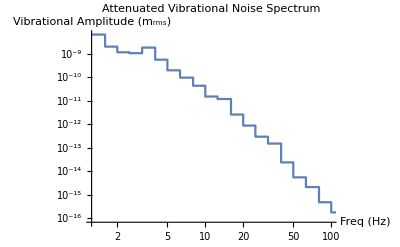

```mathematica
pltnoise2 = ListStepPlot[Transpose[{bins⟦2;;-1⟧,imulttransf[bins⟦2;;-1⟧]*data⟦2;;-1⟧}], ScalingFunctions->{"Log", "Log"}, PlotLabel->"Attenuated Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Vibrational Amplitude (m_rms)"},PlotRange->{{1.25,100},Automatic}]
```

# Vibrational Isolation - Damped Spring

## Plots

```mathematica
GraphicsGrid[{{pltnoise,Magnify[plttrans,0.6]},{plttransmult,pltnoise2}}, ImageSize->Full]
```

-Graphics-

## Optimal Parameters

We know:
m g = k Δℓ   &  ω_0 = √(k/m)   ⟹   ω_0 = √(g/Δℓ)       Q = 1/(2γ)

```mathematica
Print["Resonant Freq: ω_0 = ", Quantity[ω0//N, "Radians per Second"], "\nDamping: γ = ", γ,"\nQuality Factor: Q = ",1/(2γ), "\nSpring Stretched Length: Δℓ = ", Quantity[Round[9.8/ω0^2*100,0.1], "Centimeters"]]
```

Resonant Freq: ω_0 = 21.9911 rad/s
Damping: γ = 1.75929
Quality Factor: Q = 0.284205
Spring Stretched Length: Δℓ = 2. cm

# Material Properties

### Setup

```mathematica
konst[Y_, S_, L_]:=(S*(10^2)^2 * Y*10^9)/(L*10^2);
kS[r_, R_, N_, S_]:= r^4/(4 N R^3)S;
dataim = ImageData[Import["C:\\Users\\freem\\Documents\\GitHub\\MinusKModelling\\Resources\\legs_vert_transf2.bmp"]];
pixelData={};
For[j=1, j≤Dimensions[dataim]⟦2⟧, j++,
x={};
For[i =1 , i≤ Dimensions[dataim]⟦1⟧, i++,
dataim⟦i,j⟧ = dataim⟦i,j,1⟧;
If[dataim⟦i, j⟧≠ 1.,
x = Append[x, i];
];
];
pixelData=Append[pixelData,{j,353-Mean[x]}];
]
tAirLeg ={N[0.8*Power[10,Log10[30/0.8]/462*Transpose[pixelData]⟦1⟧]],N[Power[10,4/353 Transpose[pixelData]⟦2⟧-3]]};
outputTransferFunction[k_, γ_]:=(
(*Spring Transfer Function*)
m = 2.9;
ω0 =√(k/m);
sprtransf[f_]:=(√(4 γ^2(2π f)^6+(ω0^4-ω0^2(2π f)^2+4 γ^2(2π f)^2)^2))/((ω0^2-(2π f)^2)^2+4 γ^2(2π f)^2);
pltspr=LogLogPlot[sprtransf[f], {f, 0.8, 30}, PlotStyle->Red,PlotRange->{{0.8, 30},{0.001,10}}];

(*Spring and Air Leg Transfer Function - Separate*)
plttrans=Show[pltspr, pltairleg,PlotLabel->"Transfer Functions (Separate)",LabelStyle->13, AxesLabel->{"Freq (Hz)", "Attenuation"},AxesStyle->14, ImageSize-> 400];
plttrans = Legended[plttrans , Placed[LineLegend[{Darker[Blue], Red},{"Air Leg", "Spring"}, LabelStyle->11],Right]];

(*Together*)
multtransf = Transpose[{tAirLeg⟦1⟧,sprtransf[tAirLeg⟦1⟧]*tAirLeg⟦2⟧}];
imulttransf = Interpolation[multtransf];
plttransmult=ListLogLogPlot[multtransf, PlotLabel->"Transfer Function (Combined)", AxesLabel->{"Freq (Hz)", "Attenuation"}, PlotRange->{{0.8,30},Automatic}, Joined->True];

(*Resultant Noise*)
For[i=1,i≤ Length[tAirLeg⟦1⟧],i++,
If[tAirLeg⟦1, i⟧>100,stop=i-1;Break[]];
];
tAirLeg=Transpose[Transpose[tAirLeg]⟦1;;stop⟧];
noise2=Transpose[{tAirLeg⟦1⟧,ifun[tAirLeg⟦1⟧]*sprtransf[tAirLeg⟦1⟧]*tAirLeg⟦2⟧}];
pltnoise2 = ListStepPlot[Transpose[{bins⟦2;;-1⟧,imulttransf[bins⟦2;;-1⟧]*data⟦2;;-1⟧}], ScalingFunctions->{"Log", "Log"}, PlotLabel->"Attenuated Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Vibrational Amplitude (m_rms)"},PlotRange->{{1.25,100},Automatic}];

GraphicsGrid[{{pltnoise,Magnify[plttrans,0.6]},{plttransmult,pltnoise2}}, ImageSize->Full]
)//Quiet
```

### Applications

# | Material
1 | Spring (Music-Wire Steel,1/2" unstretched, 5108N176)
2 | Spring (Music-Wire Steel,1" unstretched, 5108N917
3 | Spring (Music-Wire Steel,6 1/2" unstretched, 5108N917)
4 | Spring (Plastic,1" unstretched, 2017N123)
5 | Spring (Beryllium Copper,1 mm wire,15 mm OD,15 turns)
6 | Spring (Brass,1 mm wire,15 mm OD,15 turns)
7 | Spring (Carbon Steel,0.9 mm wire,15 mm OD,15 turns)
8 | Hydrogel (acrylamide gel,15 cm long,1 cm area)

#### Spring (Music-Wire Steel, 1/2” unstretched, 5108N176)

```mathematica
plt1=Magnify[outputTransferFunction [QuantityMagnitude[UnitConvert[Quantity[59.5, ("PoundsForce")/("Feet")], "Newtons"/"Meters"]],3],1]
```

-Graphics-

#### Spring (Music-Wire Steel, 1” unstretched, 5108N917)

```mathematica
plt2 =Magnify[outputTransferFunction [QuantityMagnitude[UnitConvert[Quantity[50.7, ("PoundsForce")/("Feet")], "Newtons"/"Meters"]],3],1.1]
```

-Graphics-

#### Spring (Zinc-Plated Steel, 6 1/2” unstretched, 9654K563)

```mathematica
plt3 =Magnify[outputTransferFunction [QuantityMagnitude[UnitConvert[Quantity[0.62, ("PoundsForce")/("Feet")], "Newtons"/"Meters"]],3],1.1]
```

-Graphics-

#### Spring (Plastic, 1” unstretched, 2017N123)

```mathematica
plt4=Magnify[outputTransferFunction [QuantityMagnitude[UnitConvert[Quantity[23.98, ("PoundsForce")/("Feet")], "Newtons"/"Meters"]],3],1.1]
```

-Graphics-

#### Spring (Beryllium Copper, 1 mm wire, 15 mm OD, 15 turns)

```mathematica
plt5=Magnify[outputTransferFunction [kS[10^-3, 1*10^-2,15, 48*10^9],3],1.1]
```

-Graphics-

#### Spring (Brass, 1 mm wire, 15 mm OD, 15 turns)

```mathematica
plt6=Magnify[outputTransferFunction [kS[10^-3, 1*10^-2,15, 40*10^9],3],1.1]
```

-Graphics-

#### Spring (Carbon Steel, 0.9 mm wire, 15 mm OD, 15 turns)

```mathematica
plt7=Magnify[outputTransferFunction [kS[0.9*10^-3, 1*10^-2,15, 78*10^9],3],1.1]
```

-Graphics-

#### Hydrogel (acrylamide gel, 15 cm long, 1 cm area)

```mathematica
plt8 =Magnify[outputTransferFunction [konst[1*10^-6, 1, 15],3],1.1]
```

-Graphics-

### Spring Length

#### Spring (15 turns w/ damping)

```mathematica
plt7=Magnify[outputTransferFunction [kS[0.9*10^-3, 1*10^-2,15, 78*10^9],1],1.1]
```

-Graphics-

#### Spring (100 turns w/ damping)

```mathematica
plt7=Magnify[outputTransferFunction [kS[0.9*10^-3, 1*10^-2,100, 78*10^9],1],1.1]
```

-Graphics-

#### Spring (500 turns w/ damping)

```mathematica
plt7=Magnify[outputTransferFunction [kS[0.9*10^-3, 1*10^-2,500, 78*10^9],1],1.1]
```

-Graphics-

#### Spring (∞ turns w/ damping)

```mathematica
plt7=Magnify[outputTransferFunction [kS[0.9*10^-3, 1*10^-2,∞, 78*10^9],1],1.1]
```

-Graphics-

#### Spring (∞ turns, no damping)

```mathematica
plt7=Magnify[outputTransferFunction [kS[0.9*10^-3, 1*10^-2,∞, 78*10^9],0],1.1]
```

-Graphics-

# Negative-K ⇒ No Composites

## Chamberlain Vibrational Noise Data

-Graphics-

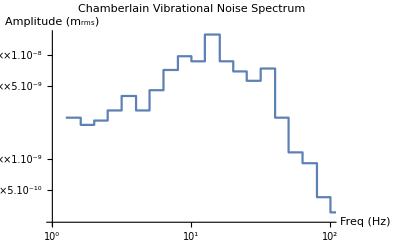

```mathematica
bins = {0,1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {0,200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
unlogch[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
data = Table[unlogch[pixels⟦i⟧],{i, 1, Length[pixels]}];
ifun=Interpolation[Transpose[{bins, data}]];
LogLogPlot[ifun[x], {x,1.25, 100}, PlotLabel->"Chamberlain Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Amplitude (m_rms)"}]
pltnoise = ListStepPlot[Transpose[{bins⟦2;;-1⟧,data⟦2;;-1⟧}], ScalingFunctions->{"Log10", "Log10"}, PlotLabel->"Chamberlain Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Amplitude (m_rms)"}, PlotRange->{{1,100},Automatic}]
```

find factor such that vibration is less than a pm, find largest one and return both factor and freq

## Transfer

To Do:
Change variables from Ω=ω/ω_0 to f

```mathematica
logRange[l_,u_,n_]:=Table[-(u-l)Log10[i]/Log10[n]+u,{i,n}];
data = logRange[0.001, 100, 2000];
```

from here

-Graphics-fig 13
     -Graphics-        -Graphics-       -Graphics--Graphics--Graphics--Graphics-ζ2 similarly

```mathematica
Options[tNSS]={"Hysteresis"->False, "kh"->2, "kv"->1,"M"->1, "Ze"->0.2, "c1"->0.04,"c2"->0.1 , "L"->0.05, "Bounds"->{0.001, 100}, "PointsPerDecade"->100};
tNSS[inp_,OptionsPattern[]]:=Block[{C1 = OptionValue["c1"],C2 = OptionValue["c2"],𝒵e = OptionValue["Ze"], m = OptionValue["M"], Kv = OptionValue["kv"], Kh=OptionValue["kh"] ,ℒ =OptionValue["L"] ,min = OptionValue["Bounds"]⟦1⟧, max=OptionValue["Bounds"]⟦2⟧,pPD=OptionValue["PointsPerDecade"],Ω,δqzs,ω0,λ,ze,A,cosθ,T, ζ1, ζ2, tdata, tdataI, tdataII, tdataIII, params, output, string, pltspr, data, ndata},
ζ1 = C1/(2 m ω0);
ζ2 = C2/(2m ω0);
ω0 = √(Kv/m);
δqzs = 2/(Kh/Kv);
λ = (2-δqzs)/(8 δqzs);
ze = 𝒵e/ℒ;
A[Ω_]:= A/.NSolve[(2ζ1 A Ω+1/8 ζ2 A^3 Ω+1/64 ζ2 A^5 Ω)^2+(3/4 λ A^3-A Ω^2)^2==ze^2 Ω^4,A,PositiveReals];
cosθ[Ω_]:= (3/4 λ A[Ω]^3-A[Ω] Ω^2)/(ze Ω^2);
T[f_]:= √((A[(2π f)/ω0]/ze)^2+2 (A[(2π f)/ω0]/ze)cosθ[(2π f)/ω0]+1);
logRange[l_,u_,n_]:=Table[-(u-l)Log10[i]/Log10[n]+u,{i,1, n}];
data={};
For[i =1, 10^i*min<10* max, i++,
minTemp= 10^(i-1)min;
maxTemp=10^i min;
ndata=Reverse[logRange[minTemp, maxTemp, pPD]];
data = Join[data,ndata];
];
data=Reverse[DeleteDuplicates[data]];

PrintTemporary["Initialization complete"];
PrintTemporary["Performing numerical calculations..."];
If[OptionValue["Hysteresis"]==True,
tdata=Reverse[Table[{data⟦i⟧,T[data⟦i⟧]}, {i, Length[data]}]];
(*divide the data into III regions*)
(*Find bounds:*)
bI=1;
bII = Length[tdata];
For[i = 1, i≤Length[tdata], i++,
If[Length[tdata⟦i,2⟧]>1,
bI=i;
Break[];
];
];
For[i = Length[tdata], i≥1, i--,
If[Length[tdata⟦i,2⟧]>1,
bII=i;
Break[];
];
];
PrintTemporary["Found bounds"];

(*region I*)
tdataI = Table[{tdata⟦i,1⟧, tdata⟦i,2,-1⟧},{i, bII}];
PrintTemporary["Calculated region I"];
If[bII!=Length[tdata],
(*region II*)
tdataII =Reverse[Table[{tdata⟦i,1⟧, tdata⟦i,2,2⟧},{i, bI,bII}]];
PrintTemporary["Calculated region II"];

(*region III*)
tdataIII = Table[{tdata⟦i,1⟧, tdata⟦i,2,1⟧},{i, bI,Length[tdata]}];
PrintTemporary["Calculated region III"];
tdata=Catenate[{tdataI,tdataII,tdataIII}];
,
tdata = tdataI;
];
,
tdata=Table[{data⟦i⟧,T[data⟦i⟧]⟦-1⟧}, {i, Length[data]}];
];
PrintTemporary["Final data set calculated"];
PrintTemporary["Finishing up..."];
output={};
If[inp == "all", string = "plot, data, params, spring", string=inp];
If[StringContainsQ[string, "plot"] == True,
	output=Append[output,ListPlot[tdata, ScalingFunctions->{"Log10", "Log10"}, Joined->True, PlotLabel->"Transfer Functions", AxesLabel->{"Freq (Hz)", "Attenuation"}]];
];
If[StringContainsQ[string, "data"] == True,
	output=Append[output,tdata]];
If[StringContainsQ[string, "params"] == True,
	params= {"ω_0 → "<>ToString[ω0//N],"δ_qzs → "<>ToString[δqzs//N],"ζ_1 → "<>ToString[ζ1//N],"ζ_2 → "<>ToString[ζ2//N]};
	output=Append[output,params]];
If[StringContainsQ[string, "spring"] == True,
	sprtransf[f_]:=(√(4 ζ1^2(2π f)^6+(ω0^4-ω0^2(2π f)^2+4 ζ1^2(2π f)^2)^2))/((ω0^2-(2π f)^2)^2+4 ζ1^2(2π f)^2);
	pltspr=LogLogPlot[sprtransf[f], {f, data⟦1⟧, data⟦-1⟧}, PlotStyle->Red,PlotRange->{{0.001, 1000},{0.001,10}}];
	output=Append[output,pltspr]];
output
]
```

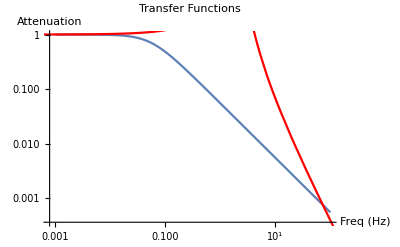

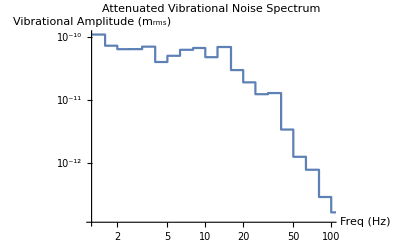

```mathematica
{NSSplt, NSSdata,params, SPRplt }=tNSS["all",Bounds->{0.001, 100},c1->1, c2->1000,kh->1000,kv->200,M->2.9,Ze->10^-8, L->0.1,Hysteresis->True, PointsPerDecade->100];
Show[ NSSplt,SPRplt]

bins = {0,1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {0,200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
unlogch[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
cdata = Table[unlogch[pixels⟦i⟧],{i, 1, Length[pixels]}];
iNSSfun=Interpolation[NSSdata];
pltnoise2 = ListStepPlot[Transpose[{bins⟦2;;-1⟧,iNSSfun[bins⟦2;;-1⟧]*cdata⟦2;;-1⟧}], ScalingFunctions->{"Log", "Log"}, PlotLabel->"Attenuated Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Vibrational Amplitude (m_rms)"},PlotRange->{{1.25,100},Automatic}]
```

```mathematica
Out[816]
```

-Graphics-